```mathematica
SetDirectory[NotebookDirectory[]];
```

## Bset 2 - Nathan Yee

## Question 1 - handel again

### d)

```mathematica
handel=Transpose[Import["Files/handel.csv","Data"]][[1]]
```

{0,-0.0061568,-0.075036,-0.031169,0.0061568,0.038095,0.018855,-0.025012,-0.031169,-0.075036,-0.12583,-0.1443,-0.18124,-0.19048,73085,0.13199,0.018855,-0.081193,-0.1443,-0.19048,-0.1443,-0.062722,0.018855,0.15046,0.16277,0.12583,0.22742,0.15046,0}
 |  |  |  |

```mathematica
handel3Avg=ListConvolve[Table[1/3,{3}],handel]
```

{-0.0270643,-0.0374539,-0.0333494,0.00436093,0.0210356,0.010646,-0.012442,73097,-0.0627223,0.035531,0.110695,0.146353,0.172007,0.167903,0.12596}
 |  |  |  |

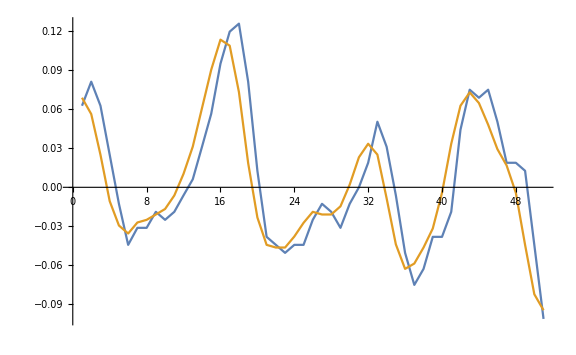

```mathematica
ListLinePlot[{handel[[1000;;1050]],handel3Avg[[1000;;1050]]},ImageSize->Large]
```

```mathematica
ListPlay[handel,SampleRate->8192]
ListPlay[handel3Avg,SampleRate->8192]
```

-Graphics-

-Graphics-

#### The avg sound sounds much more muffled and smoothed out than the original

### e)

```mathematica
Rasterize@ListLinePlot[Table[RotateRight[Abs[Fourier[data]],Floor@(Length[data]/2)],{data,{handel,handel3Avg}}],PlotRange->Full,ImageSize->Large]
```

-Graphics-

#### We can see in the above plot

## Question 2 - disturbance in the force

```mathematica
indexLargest[soundData_]:=(Position[Re[soundData],Max[Re[soundData]]][[1]])
NotchFilter[Ω0_,q_,Ω_]:=(((1−E^(−I(Ω0+Ω)))(1−E^(−I(Ω−Ω0))))/((1-q*E^(−I(Ω0+Ω)))(1−q*E^(−I(Ω−Ω0)))))
```

```mathematica
x275=Import["Files/Disturbance275.wav","Data"];
x261=Import["Files/Disturbance261.wav","Data"];
xOrig=Import["Files/DisturbanceOrig.wav","Data"];
Fs2=22050;
```

```mathematica
disturbances={x275,x261,xOrig};
names={"x275","x261","xOrig"};
```

```mathematica
Grid[{names,Table[ListPlay[soundData,SampleRate->Fs2],{soundData,disturbances}]}]
```

x275 | x261 | xOrig
-Graphics- | -Graphics- | -Graphics-

```mathematica
Rasterize@ListLinePlot[Table[RotateRight[Abs[Fourier[soundData]],Floor@(Length[soundData]/2)],{soundData,disturbances}],PlotRange->Full,ImageSize->Large]
```

-Graphics-

#### Two extreme values show in plot below. Set these to zero and get back sound data

{0.00409717-0.0021909 ⅈ,-0.00112833-0.001021 ⅈ,0.00182203-0.000320854 ⅈ,39996,-0.00112833+0.001021 ⅈ,0.00409717+0.0021909 ⅈ}
 |  |  |  |

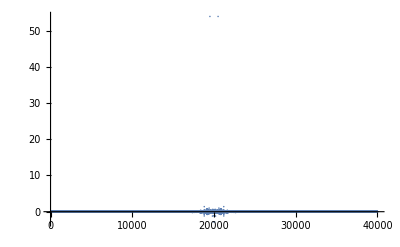

```mathematica
x275IDFT=RotateRight[Fourier[x275],Floor@(Length[x275]/2)]
ListPlot[Re[x275IDFT],PlotRange->All]
```

{0,0}

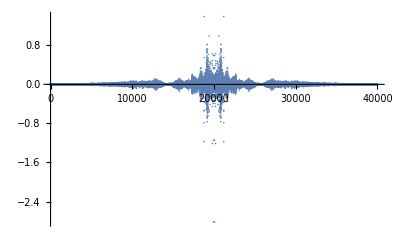

```mathematica
Table[x275IDFT[[indexLargest[x275IDFT]]]=0,{i,2}]
ListPlot[Re[x275IDFT],PlotRange->All]
```

```mathematica
ListPlay[Re[InverseFourier[RotateLeft[x275IDFT,Floor@(Length[x275IDFT]/2)]]],SampleRate->Fs2]
```

-Graphics-

### a) ii - Use notch filter to filter our noise

```mathematica
y[n]=Ay[n−1]+By[n−2]+Px[n]+Qx[n−1]+Rx[n−2]
```

Ay[-1+n]+By[-2+n]+Px[n]+Qx[-1+n]+Rx[-2+n]

```mathematica
x275
```

{0.332102,0.351176,0.380779,0.414045,0.430219,0.436323,0.439344,39988,0.432386,0.44322,0.457869,0.462477,0.470748,0.468825}
 |  |  |  |

```mathematica
Ω=2Pi*275.6181/Fs2;
q=.95;
A=2*q*Cos[Ω];
B=−q^2;
P=1;
Q=(-2)Cos[Ω];
R=1;
smallList=x275;
largeListMutable=Join[{0,0}, smallList,{0,0}];
largeListImmutable=Join[{0,0}, smallList,{0,0}];
Do[largeListMutable[[i+2]]=
A*largeListMutable[[i+1]]+
B*largeListMutable[[i]]+
P*largeListMutable[[i+2]]+
Q*largeListMutable[[i+1]]+
R*largeListMutable[[i]],
{i,1,Length[smallList]}]
largeListMutable[[1;;100]]
```

{0,0,0.332102,0.318069,0.381451,0.407029,0.426833,0.433457,0.437749,0.431069,0.415552,0.397129,0.382529,0.357987,0.332642,0.297558,0.254699,0.196284,0.151266,0.109286,0.0744429,0.0455937,0.0303932,0.000591464,-0.0330759,-0.0672931,-0.12176,-0.187111,-0.238213,-0.290302,-0.339164,-0.386491,-0.431489,-0.488075,-0.533788,-0.585956,-0.619758,-0.653091,-0.660815,-0.674801,-0.668575,-0.668606,-0.662747,-0.661686,-0.670101,-0.674713,-0.663568,-0.657408,-0.646102,-0.625937,-0.603286,-0.591188,-0.575262,-0.537645,-0.506579,-0.463863,-0.421208,-0.375886,-0.322656,-0.282772,-0.239994,-0.198286,-0.155945,-0.120669,-0.0641186,-0.0178548,0.0307468,0.0771056,0.129531,0.165813,0.209454,0.255761,0.293426,0.343718,0.389375,0.427112,0.469276,0.500339,0.516032,0.535899,0.550647,0.556119,0.558659,0.564219,0.558938,0.544808,0.527299,0.506091,0.474911,0.441435,0.404347,0.36471,0.322472,0.270937,0.217908,0.176024,0.124246,0.0799126,0.0325906,-0.0146836}

#### I couldn’t get this to work. I think I’ll move on from this problem because it’s taking way too much time.

```mathematica
ListPlay[largeListMutable,SampleRate->Fs2]
```

-Graphics-

## Question 3

```mathematica
x[t_]=E^(-t/T)
```

```mathematica
Integrate[E^(-t/T),{t,-Infinity,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(-t/T) does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-t/T)ⅆt